# Quantum Fourier Transform: Implementation

This  is  a demonstration material accompanying the corresponding YouTube video.

Episodes 32. Quantum Fourier Transform: Principle

Episodes 33. Quantum Fourier Transform: Implementation

NOTICE: Q3 has been updated the YouTube video was taken, and accordingly, this notebook has been updated as well.

## What do we mean?

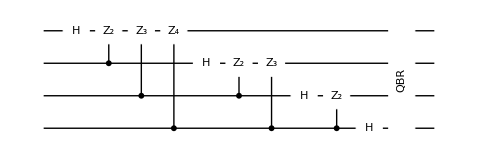
=-Graphics-

Figure 1. Implementation of quantum Fourier transform (QFT) by means of elementary gates, where QBR is the quantum bit-reversal transform and Z_k denotes the phase gate by phase angle 2π/2^k; that is,
	Z_k:=(1 | 0
0 | ⅇ^(ⅈ2π/2^k)) .

## Simple Property

### Example

```mathematica
Let[Qubit,S]
```

```mathematica
$n=3;
$N=Power[2,$n];
SS=S[Range[$n],$]
```

```mathematica
in=Basis[SS]
```

```mathematica
mat=FourierMatrix[$N];
```

```mathematica
out=in.mat;
```

```mathematica
KetFactor[out[[3]]]
```

### Summary

For any computational basis state, the  quantum Fourier transform gives a product state.

X_y:=y_1⊗y_2⊗…⊗y_n

X_y↦P_y=((0+1 ⅇ^(2π ⅈ 0. y_n))/(√2))⊗((0+1 ⅇ^(2π ⅈ 0. y_(n-1)y_n))/(√2))⊗⋯⊗((0+1 ⅇ^(2π ⅈ 0. y_1 y_2(⋯y)_n))/(√2)).

## Quantum Implementation

```mathematica
Let[Qubit,S]
```

```mathematica
$n=4;
$N=Power[2,$n];
SS=S[Range[$n],$]
```

The unitary operator corresponding to the quantum Fourier transform.

```mathematica
op=QFT[SS]
```

```mathematica
qc=QuantumCircuit[op]
```

```mathematica
mat=Matrix[qc]
```

```mathematica
mat[[;;UpTo[10],;;UpTo[10]]]//MatrixForm
```

Implement the quantum Fourier transform by means of elementary gates.

```mathematica
new=QuantumCircuit[UnfoldAll@qc]
```

Here, QBR is the quantum bit-reversal transform, and Z_k denotes the phase gate by angle 2π/2^k; that is,

Z_k:=(1 | 0
0 | ⅇ^(ⅈ2π/2^k))

To verify the implementation, calculate the matrix representation of the new quantum circuit.

```mathematica
more=Matrix[new]
```

Compare the two matrices.

```mathematica
more-mat//SimplifyThrough//MatrixForm
```

## Summary

### Keywords

Fourier transform

Discrete Fourier transform

Quantum Fourier transform

### Functions

ControlledGate

Fourier

QFT

### Related Links

Section 4.3 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Fourier Transform

Full List of Demonstrations in YouTube Videos

## Epilog